{{x[t]→c ⅇ^t}}

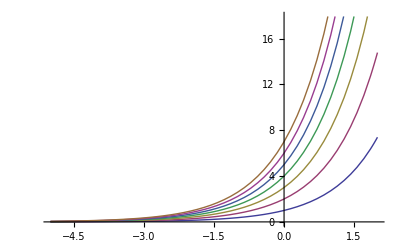

```mathematica
Clear[f,x,t]
f = x[t];
table = {1,2,3,4,5,6,7};
DSolve[{x'[t] == f,x[0]==c},x[t],t]
(*Table[Plot[f[c],{t,-3,3}],{c,1,5}]*)
Plot[Evaluate[x[t]/.%/.c-> table],{t,-5,2}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x[t]→(c ⅇ^t)/(1-c+c ⅇ^t)}}

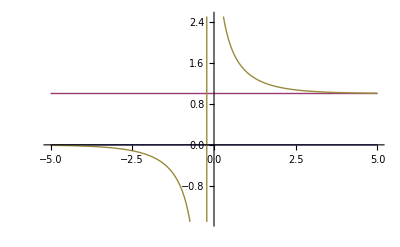

```mathematica
Clear[f,x,t]
f =x[t](1-x[t]);
table = {0,1,5};
DSolve[{x'[t] == f,x[0]==c},x[t],t]
(*Table[Plot[f[c],{t,-3,3}],{c,1,5}]*)
Plot[Evaluate[x[t]/.%/.c-> table],{t,-5,5}]
```

```mathematica
FixedPoint[Cos,1.0]
```

```mathematica
$Aborted
```

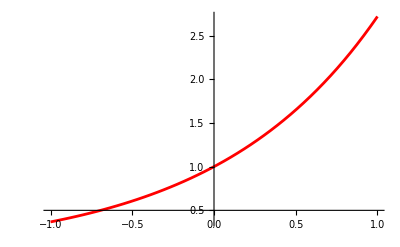

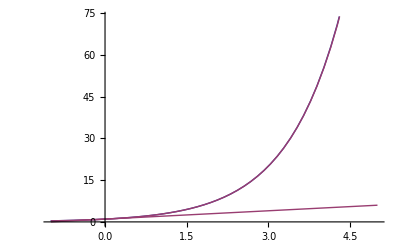

```mathematica
Plot[Exp[x],{x,-1,1},PlotStyle->{Thickness[0.005],RGBColor[1,0,0]}]
Plot[{Exp[x],Sum[x^k/Factorial[k],{k,0,m}]/.m->{1,10}},{x,-1,5}]
```